## Simple example of using the KerrTTML` package to compute Left Total-Transmission Modes of the Kerr geometry

### Load the KerrTTML` package

```mathematica
Needs["KerrTTML`"]
```

### You must choose whether to use the Polynomial or Continued Fraction for solving the radial equation .

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

### You must choose the spin weight of the modes you will compute . In this case, we are computing gravitational TTMLs .

```mathematica
SetSpinWeight[-2];
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

### Create a minimal table of Schwarzschild gravitational TTMLs for use as initial guesses.

```mathematica
For[l=2,l<=5,++l,
SchTTMLTable[l,0]={-ⅈ/12(l-1)l(l+1)(l+2),0};
SchTTMLTable[l,1]={-ⅈ/12(l-1)l(l+1)(l+2),1};
SchTTMLTable[l]=2;
]
```

```mathematica
For[l=2,l<=5,++l,
	SchwarzschildTTML[l,0];
]
```

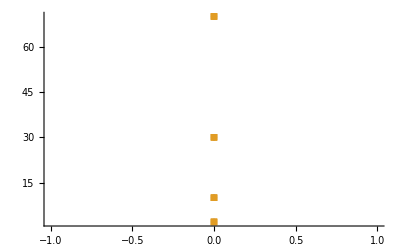

```mathematica
Show[Table[PlotSchTTML[l],{l,2,5}],PlotRange->All]
```

### Create the ℓ=2, m=0, n=0 TTML sequence to an accuracy of 10^-5.

```mathematica
KerrTTMLSequence[2,0,0,-5]
```

### Plot the mode frequencies and separation constant values along the ℓ = 2, m = 0, n = 0 sequence .

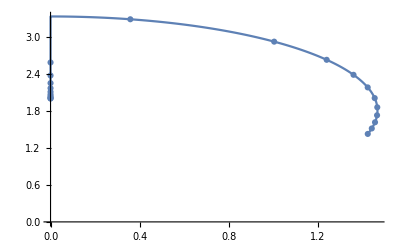

```mathematica
ModePlotOmega[2,0,0]
```

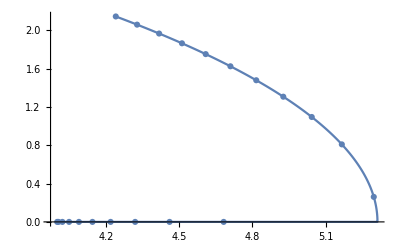

```mathematica
ModePlotA[2,0,0]
```

#### Notice that the mode has a non - smooth change in direction . We can split this sequence into two overtone multiplets.

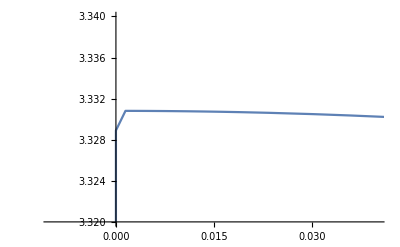

```mathematica
ModePlotOmega[2,0,0,PlotRange->{{-0.01,0.04},{3.32,3.34}}]
```

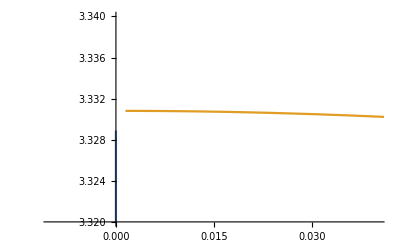

```mathematica
ListLinePlot[{Take[KerrOmegaList[2,0,0],571],Drop[KerrOmegaList[2,0,0],571]},PlotRange->{{-0.01,0.04},{3.32,3.34}}]
```

#### First, turn the sequence into a multiplet with a single overtone.

```mathematica
KerrModeMakeMultiplet[2,0,0]
```

```mathematica
ModePlotOmega[2,0,{0,0},PlotRange->{{-0.01,0.04},{3.32,3.34}}]
```

-Graphics-

#### Next, split the sequence at the discontinuity saving each as a separate overtone multiplet.

```mathematica
{KerrTTML[2,0,{0,0}],KerrTTML[2,0,{0,1}]}=TakeDrop[KerrTTML[2,0,{0,0}],571];
```

#### Now we can plot the sequence again as an overtone multiplet.

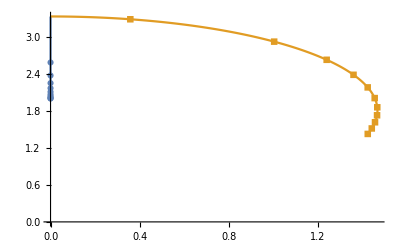

```mathematica
ModePlotOmega[2,0,OTmultiple->{{0,2}}]
```

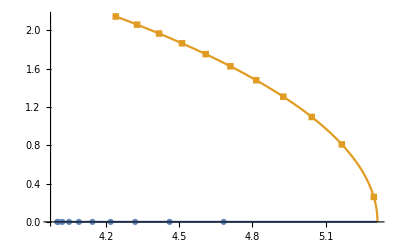

```mathematica
ModePlotA[2,0,OTmultiple->{{0,2}}]
```